```mathematica
CSUgreen=RGBColor["#1E4D2B"];
CSUgold=RGBColor["#C8C372"];
CSUorange=RGBColor[.85,.47,.176];
a=Pi/2;
distribution = Rectangle[{-.01,-.5},{.01,.5}];
Animate[Graphics[{CSUgreen,distribution,CSUgold,Rectangle[{-.01+t,-.5},{.01+t,.5}],Text[θ,{t/2,-.6}]},Axes-> True,PlotRange->{{-1,1},{-.75,.75}}],{t,-1,1,.03},AnimationDirection->ForwardBackward]
```

```mathematica
comparoGIF=Table[Graphics[{CSUgreen,distribution,CSUgold,Rectangle[{-.01+t,-.5},{.01+t,.5}]},Axes-> True,PlotRange->{{-1,1},{-.75,.75}}],{t,-1,1,.03}];
Export["~/Documents/website/remark/wasserstein_gan/comparison_gif.gif",comparoGIF,"AnimationRepetitions"->Infinity]
```

~/Documents/website/remark/wasserstein_gan/comparison_gif.gif

```mathematica
gif=Table[Graphics[{manifold,Disk[{Cos[fm],Sin[fm]},diskSize],CSUgreen,Opacity[.7],Disk[{Cos[(1-t)*a+t*fm],Sin[(1-t)*a+t*fm]},diskSize],Disk[{Cos[(1-t)*b+t*fm],Sin[(1-t)*b+t*fm]},diskSize],Disk[{Cos[(1-t)*c+t*fm],Sin[(1-t)*c+t*fm]},diskSize],Triangle[{{Cos[(1-t)*a+t*fm],Sin[(1-t)*a+t*fm]},{Cos[(1-t)*b+t*fm],Sin[(1-t)*b+t*fm]},{Cos[(1-t)*c+t*fm],Sin[(1-t)*c+t*fm]}}],CSUgold,Opacity[1],Disk[(1/3)*{Cos[(1-t)*a+t*fm],Sin[(1-t)*a+t*fm]}+(1/3)*{Cos[(1-t)*b+t*fm],Sin[(1-t)*b+t*fm]}+(1/3)*{Cos[(1-t)*c+t*fm],Sin[(1-t)*c+t*fm]},diskSize]},PlotRange->{{0,1.2},{0,1.2}}],{t,0,1,.01}];
Export["homotopy.gif",homotopy,"AnimationRepetitions"->Infinity]
Export["homotopy2.gif",gif,"AnimationRepetitions"->Infinity]
```

homotopy.gif

homotopy2.gif

```mathematica
aPoint = {Cos[a],Sin[a]};
bPoint = {Cos[b],Sin[b]};
cPoint = {Cos[c],Sin[c]};
fPoint = {Cos[fm],Sin[fm]};
oldHomotopy = Animate[Graphics[{manifold,Disk[fPoint,diskSize],CSUgreen,Opacity[.7],Disk[aPoint,diskSize],Disk[bPoint,diskSize],Disk[cPoint,diskSize],Opacity[.3],EdgeForm[{Thick,CSUgreen}],Triangle[{aPoint,bPoint,fPoint}],Triangle[{aPoint,cPoint,fPoint}],Triangle[{bPoint,cPoint,fPoint}],Triangle[{aPoint,cPoint,bPoint}],CSUgold,Opacity[1],EdgeForm[],Disk[((1/3)*aPoint+(1/3)*bPoint+(1/3)*cPoint)*(1-t)+t*fPoint,diskSize],CSUgreen,Thick,Line[{aPoint,cPoint}]},PlotRange->{{-.1,1.2},{-.1,1.2}}],{t,0,1},AnimationDirection->ForwardBackward]
```

```mathematica
Export["oldHomotopy.gif",oldHomotopy,"AnimationRepetitions"->Infinity]
```

oldHomotopy.gif

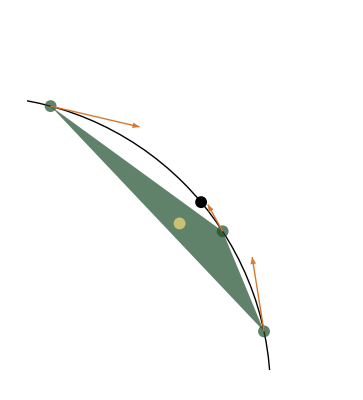

tangentSpace.png

```mathematica
t=.3;
tangentSpace = Graphics[{manifold,Disk[{Cos[fm],Sin[fm]},diskSize],CSUgreen,Opacity[.7],Disk[{Cos[(1-t)*a+t*fm],Sin[(1-t)*a+t*fm]},diskSize],Disk[{Cos[(1-t)*b+t*fm],Sin[(1-t)*b+t*fm]},diskSize],Disk[{Cos[(1-t)*c+t*fm],Sin[(1-t)*c+t*fm]},diskSize],Triangle[{{Cos[(1-t)*a+t*fm],Sin[(1-t)*a+t*fm]},{Cos[(1-t)*b+t*fm],Sin[(1-t)*b+t*fm]},{Cos[(1-t)*c+t*fm],Sin[(1-t)*c+t*fm]}}],CSUgold,Opacity[1],Disk[(1/3)*{Cos[(1-t)*a+t*fm],Sin[(1-t)*a+t*fm]}+(1/3)*{Cos[(1-t)*b+t*fm],Sin[(1-t)*b+t*fm]}+(1/3)*{Cos[(1-t)*c+t*fm],Sin[(1-t)*c+t*fm]},diskSize],Thick,CSUorange,Arrow[{{Cos[(1-t)*a+t*fm],Sin[(1-t)*a+t*fm]},{Cos[(1-t)*a+t*fm],Sin[(1-t)*a+t*fm]}+{.3,-.07}}],Arrow[{{Cos[(1-t)*b+t*fm],Sin[(1-t)*b+t*fm]},{Cos[(1-t)*b+t*fm],Sin[(1-t)*b+t*fm]}+{-.04,.25}}],Arrow[{{Cos[(1-t)*c+t*fm],Sin[(1-t)*c+t*fm]},{Cos[(1-t)*c+t*fm],Sin[(1-t)*c+t*fm]}+{-.05,.09}}]},PlotRange->{{.2,1.2},{.1,1.2}}]
Export["tangentSpace.png",tangentSpace]
```

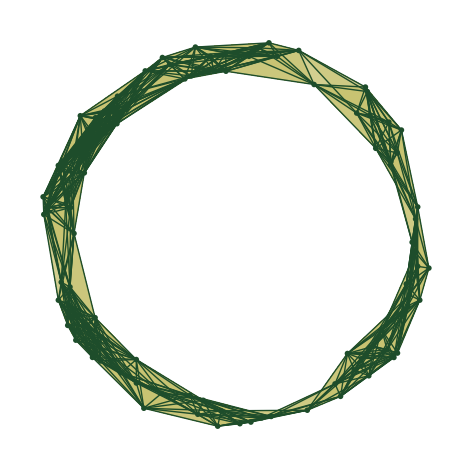

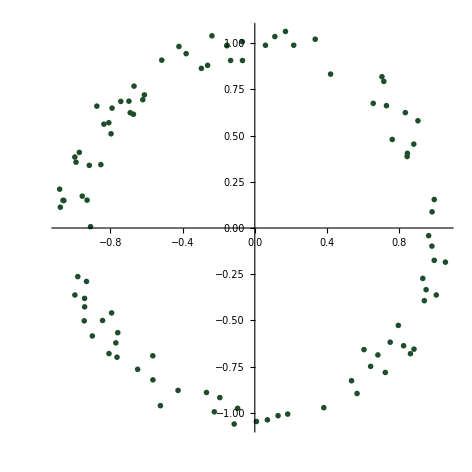

```mathematica
numPoints=100;
SeedRandom[69];
marker=Graphics[{CSUgreen,Disk[]}];
A = RandomReal[{0,2*Pi},numPoints];
X2d=Transpose[{Cos[A]+RandomReal[{-.1,.1},numPoints],Sin[A]+RandomReal[{-.1,.1},numPoints]}];
r=.5;
vertices=ListPlot[X2d,AspectRatio->1,PlotMarkers->{marker,.02}];
diam2[x_]:=Norm[x[[1]]-x[[2]]]
diam3[x_]:=Max[{Norm[x[[1]]-x[[2]]],Norm[x[[1]]-x[[3]]],Norm[x[[2]]-x[[3]]]}]
edges=Select[Subsets[X2d,{2}],diam2[#]<r&];
twosimplices=Select[Subsets[X2d,{3}],diam3[#]<r&];
simplices=Graphics[{Opacity[.4],CSUgold,Triangle[twosimplices],Opacity[1],CSUgreen,Line[edges]}];
Show[{simplices,vertices}]
Show[vertices]
```

```mathematica
(*We could do a 3D version of the above*)
Z=RandomReal[{-.01,.01},numPoints];
X=Transpose[{Cos[A],Sin[A],Z}];
ListPointPlot3D[X]
```

1.6944

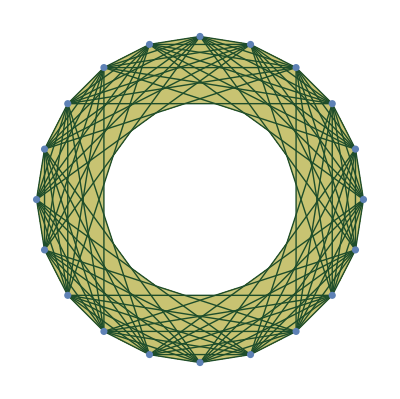

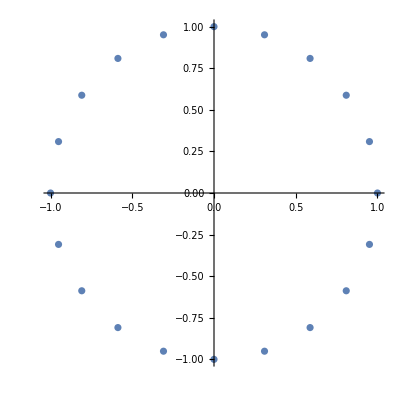

```mathematica
B=Range[0,2*Pi,.31416];
r=2*Pi/3-.4
circleX=Transpose[{Cos[B],Sin[B]}];
edgesCircle=Select[Subsets[circleX,{2}],diam2[#]<r&];
verticesCircle=ListPlot[circleX,AspectRatio->1,PlotStyle->Thick];
twosimplicesCircle=Select[Subsets[circleX,{3}],diam3[#]<r&];
simplicesCircle=Graphics[{Opacity[.4],CSUgold,Triangle[twosimplicesCircle],Opacity[1],CSUgreen,Line[edgesCircle]}];
Show[{simplicesCircle,verticesCircle}]
Show[verticesCircle]
```

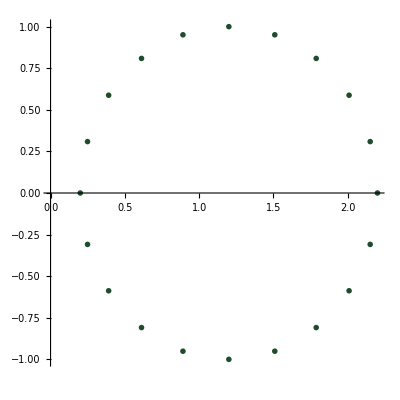

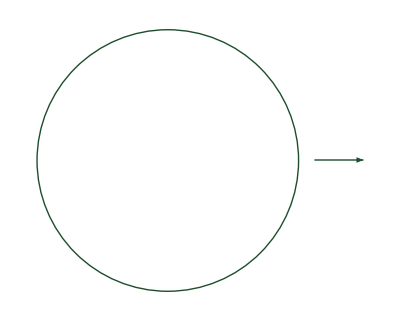

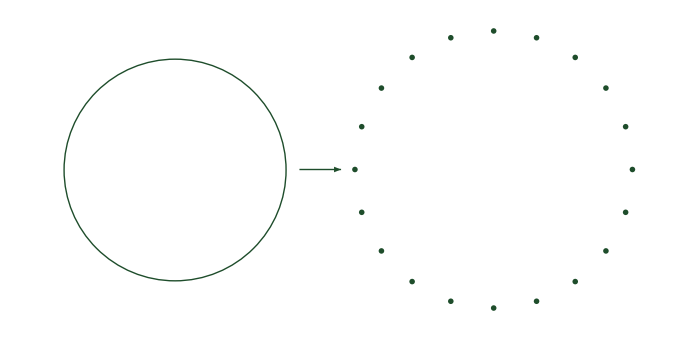

```mathematica
circleXshift = Transpose[{Cos[B]+1.2,Sin[B]}];
verticesCircleShift=ListPlot[circleXshift,AspectRatio->1,PlotMarkers->{marker,.03}]
leftCircle=Graphics[{CSUgreen,Circle[{-1.1,0},0.8],Arrow[{{-.2,0},{.1,0}}]}]
Show[{leftCircle,verticesCircleShift}]
```